```mathematica
aapl=FinancialData["NASDAQ:AAPL","Price",All]
```

TimeSeries[…]

```mathematica
TimeSeriesModelFit[aapl]
```

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

TimeSeriesModel[…]

```mathematica
2
```

2

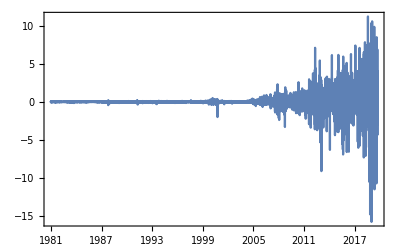

```mathematica
DateListPlot[
Transpose[{
aapl["Dates"][[;;-2]],
Differences@aapl["Values"]
}]
,ImageSize->Full,PlotRange->Full,PlotTheme->"Detailed"]
```

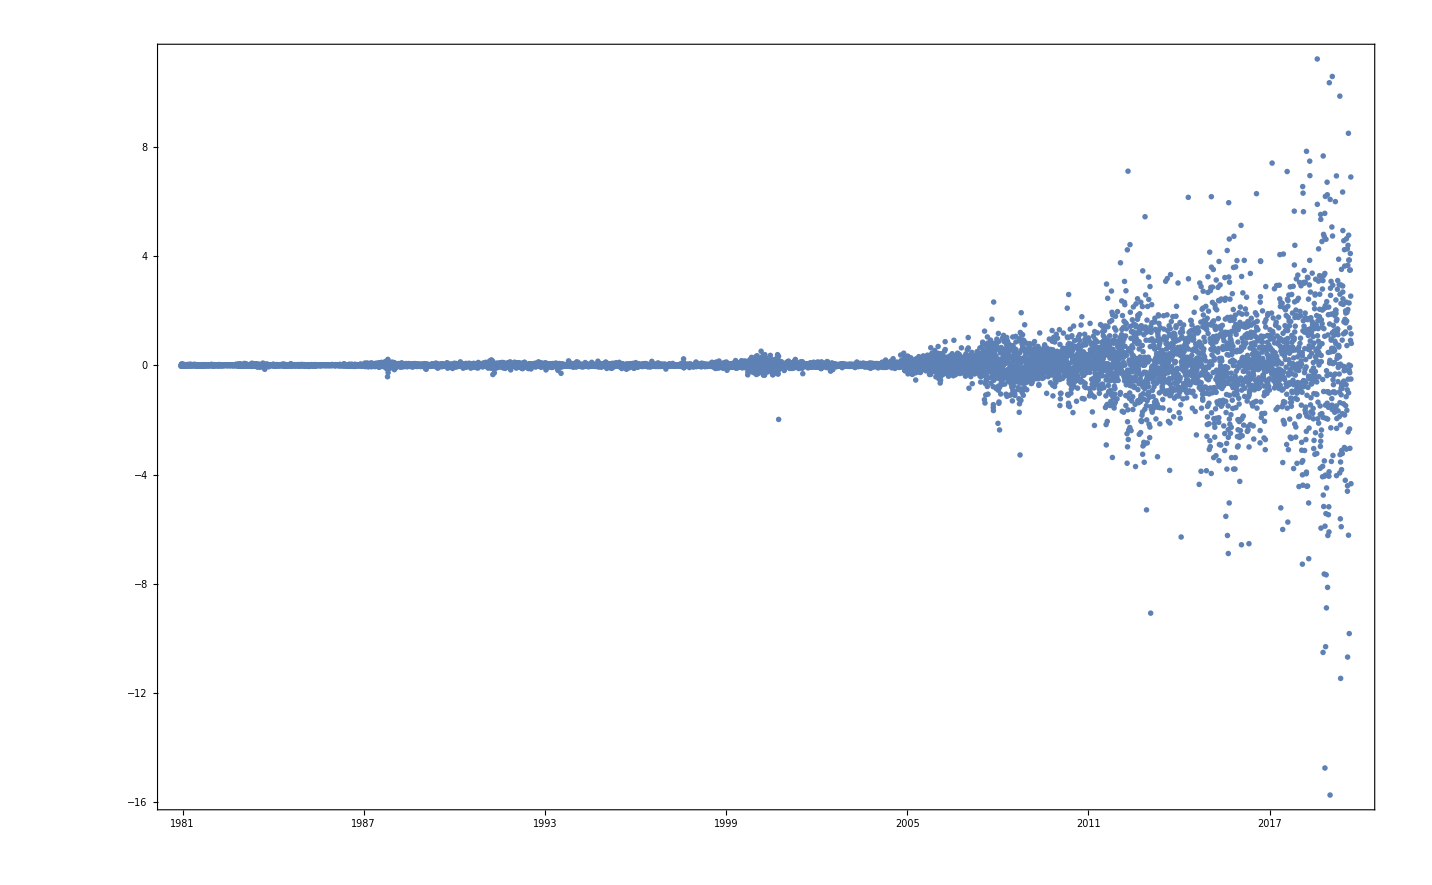

```mathematica
DateListPlot[
Transpose[{
aapl["Dates"][[;;-2]],
Differences@aapl["Values"]
}]
,ImageSize->Full,PlotRange->Full,PlotTheme->"Detailed",ColorFunction->"DarkRainbow",Joined->False]
```

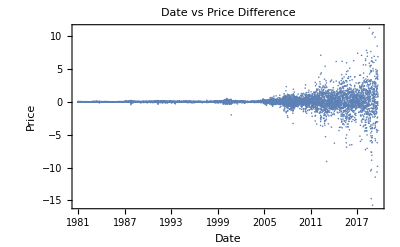

```mathematica
Show[%5,FrameLabel->{{HoldForm[Price],None},{HoldForm[Date],None}},PlotLabel->HoldForm[Date vs Price Difference],LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Grid@
TakeLargestBy[
Transpose[{
aapl["Dates"][[;;-2]],
Differences@aapl["Values"]
}],First,10]
```

Mon 16 Sep 2019 00:00:00GMT-7. | 0.80 $
Fri 13 Sep 2019 00:00:00GMT-7. | 1.15 $
Thu 12 Sep 2019 00:00:00GMT-7. | -4.34 $
Wed 11 Sep 2019 00:00:00GMT-7. | -0.50 $
Tue 10 Sep 2019 00:00:00GMT-7. | 6.89 $
Mon 9 Sep 2019 00:00:00GMT-7. | 2.53 $
Fri 6 Sep 2019 00:00:00GMT-7. | 0.91 $
Thu 5 Sep 2019 00:00:00GMT-7. | -0.02 $
Wed 4 Sep 2019 00:00:00GMT-7. | 4.09 $
Tue 3 Sep 2019 00:00:00GMT-7. | 3.49 $

```mathematica
Total@
Map[Last,
TakeLargestBy[
Transpose[{
aapl["Dates"][[;;-2]],
Differences@aapl["Values"]
}],First,10]
]
```

15.00 $

```mathematica
Partition[Range@10,2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Map[
Total,
Partition[
Differences@aapl["Values"]
,5]
]
```

{-0.01 $,0.14 $,-0.07 $,-0.03 $,0.02 $,0.00 $,-0.08 $,-0.01 $,0.00 $,-0.04 $,0.01 $,-0.08 $,0.07 $,0.01 $,-0.03 $,0.05 $,-0.01 $,0.04 $,-0.01 $,-0.01 $,-0.00 $,0.02 $,0.08 $,-0.02 $,0.01 $,-0.03 $,-0.03 $,-0.07 $,-0.06 $,0.06 $,-0.03 $,0.02 $,0.00 $,-0.04 $,-0.05 $,0.00 $,0.00 $,-0.02 $,-0.02 $,-0.06 $,0.05 $,0.04 $,-0.01 $,0.01 $,0.02 $,-0.03 $,-0.01 $,0.00 $,0.01 $,0.00 $,-0.00 $,0.06 $,-0.00 $,-0.06 $,-0.00 $,0.03 $,-0.01 $,-0.01 $,-0.02 $,0.00 $,-0.01 $,-0.03 $,-0.02 $,0.02 $,-0.01 $,0.03 $,-0.00 $,-0.01 $,-0.03 $,-0.01 $,0.03 $,-0.03 $,-0.01 $,-0.00 $,-0.02 $,0.00 $,-0.01 $,0.00 $,-0.03 $,0.01 $,0.04 $,-0.02 $,-0.01 $,0.01 $,0.01 $,0.03 $,0.04 $,-0.00 $,0.01 $,0.00 $,-0.01 $,0.03 $,0.06 $,0.03 $,-0.00 $,0.10 $,0.00 $,0.01 $,-0.03 $,0.05 $,-0.02 $,-0.05 $,0.06 $,-0.04 $,-0.04 $,0.10 $,0.08 $,0.06 $,0.05 $,0.04 $,-0.02 $,0.00 $,-0.03 $,-0.04 $,0.05 $,-0.03 $,-0.02 $,0.01 $,0.10 $,0.03 $,0.01 $,0.10 $,-0.05 $,0.10 $,0.00 $,0.05 $,-0.08 $,-0.04 $,-0.12 $,0.01 $,-0.02 $,-0.09 $,-0.09 $,-0.02 $,-0.01 $,-0.02 $,-0.05 $,0.13 $,-0.10 $,-0.03 $,0.04 $,-0.17 $,-0.01 $,0.01 $,-0.05 $,0.01 $,0.01 $,-0.04 $,0.02 $,0.00 $,-0.01 $,0.03 $,0.06 $,-0.00 $,0.02 $,0.04 $,0.02 $,-0.02 $,-0.04 $,-0.01 $,0.03 $,0.03 $,-0.02 $,0.00 $,0.00 $,-0.01 $,-0.01 $,-0.02 $,0.00 $,0.06 $,-0.01 $,0.10 $,0.00 $,-0.05 $,-0.00 $,-0.02 $,-0.01 $,0.00 $,0.00 $,-0.05 $,-0.02 $,0.02 $,-0.02 $,0.03 $,0.00 $,0.02 $,-0.02 $,0.01 $,-0.03 $,-0.00 $,0.04 $,-0.04 $,-0.04 $,0.01 $,-0.02 $,0.02 $,-0.01 $,0.00 $,-0.01 $,-0.04 $,0.05 $,0.00 $,0.03 $,0.04 $,-0.02 $,0.01 $,0.03 $,-0.03 $,0.02 $,0.00 $,0.02 $,-0.04 $,0.00 $,-0.05 $,-0.06 $,0.02 $,-0.01 $,-0.00 $,-0.02 $,0.00 $,0.03 $,-0.01 $,-0.03 $,0.00 $,0.03 $,-0.06 $,-0.04 $,0.00 $,-0.02 $,0.04 $,0.02 $,-0.01 $,-0.00 $,-0.02 $,-0.00 $,-0.02 $,0.00 $,0.00 $,0.00 $,-0.01 $,0.01 $,0.01 $,-0.01 $,-0.00 $,-0.01 $,0.05 $,0.00 $,0.02 $,0.00 $,0.00 $,-0.01 $,0.02 $,0.00 $,-0.00 $,0.04 $,-0.00 $,-0.00 $,0.01 $,0.02 $,-0.03 $,0.03 $,0.00 $,0.00 $,0.04 $,-0.03 $,0.00 $,0.04 $,0.02 $,-0.01 $,-0.00 $,0.02 $,0.02 $,0.01 $,0.02 $,0.10 $,0.00 $,0.00 $,0.03 $,-0.05 $,-0.02 $,0.02 $,0.02 $,-0.01 $,-0.10 $,0.04 $,-0.05 $,0.00 $,0.07 $,0.01 $,0.01 $,-0.04 $,-0.03 $,0.04 $,-0.05 $,0.03 $,0.01 $,-0.03 $,0.02 $,0.02 $,0.01 $,0.02 $,0.03 $,0.06 $,0.02 $,0.00 $,-0.01 $,-0.03 $,0.08 $,0.09 $,0.05 $,0.03 $,-0.00 $,0.08 $,0.05 $,0.16 $,-0.05 $,-0.07 $,0.08 $,-0.06 $,0.12 $,-0.03 $,0.02 $,0.07 $,0.08 $,-0.05 $,-0.02 $,0.04 $,-0.01 $,0.02 $,0.08 $,-0.01 $,-0.03 $,-0.12 $,0.24 $,-0.05 $,-0.05 $,0.08 $,0.20 $,0.04 $,0.07 $,0.00 $,0.06 $,-0.06 $,0.16 $,0.06 $,-0.14 $,-0.08 $,-0.54 $,-0.03 $,0.07 $,0.03 $,-0.15 $,0.02 $,-0.15 $,0.12 $,0.23 $,-0.01 $,0.16 $,-0.09 $,0.03 $,-0.11 $,0.05 $,-0.05 $,0.08 $,0.01 $,0.09 $,0.07 $,-0.02 $,-0.13 $,-0.11 $,0.04 $,-0.04 $,0.00 $,0.07 $,0.01 $,-0.07 $,-0.03 $,0.01 $,0.13 $,0.05 $,0.01 $,0.01 $,0.05 $,-0.05 $,0.01 $,-0.10 $,0.08 $,-0.04 $,-0.10 $,-0.05 $,0.04 $,-0.07 $,0.08 $,0.02 $,0.07 $,1166,-1.50 $,-2.54 $,2.99 $,0.39 $,-1.67 $,2.80 $,0.92 $,2.39 $,0.42 $,-0.61 $,5.15 $,1.76 $,5.80 $,0.51 $,4.20 $,-1.68 $,8.41 $,1.85 $,2.16 $,0.96 $,-0.22 $,-5.05 $,2.89 $,-3.70 $,-1.61 $,-5.77 $,5.03 $,-0.62 $,2.76 $,-0.88 $,1.14 $,0.27 $,4.27 $,-1.00 $,-0.44 $,-1.26 $,3.93 $,1.06 $,5.02 $,1.50 $,-0.10 $,-2.05 $,5.90 $,-4.05 $,-1.75 $,-3.64 $,1.99 $,-5.21 $,-1.34 $,-3.02 $,-5.71 $,2.57 $,3.15 $,-6.31 $,-0.00 $,-1.78 $,-1.61 $,1.71 $,-0.96 $,-2.90 $,-7.17 $,-1.07 $,5.37 $,-2.85 $,-1.57 $,-2.55 $,-0.39 $,3.72 $,0.95 $,-4.16 $,0.53 $,-4.70 $,0.38 $,4.83 $,3.51 $,-5.00 $,1.79 $,1.46 $,-1.87 $,-0.36 $,-2.73 $,-3.29 $,3.38 $,1.30 $,-0.22 $,2.29 $,3.08 $,-1.16 $,6.84 $,-0.19 $,-1.97 $,2.71 $,-8.01 $,5.79 $,-1.98 $,1.57 $,1.18 $,3.62 $,1.22 $,-0.45 $,-1.10 $,-0.06 $,0.73 $,6.08 $,-0.11 $,-1.51 $,1.81 $,-2.08 $,-2.37 $,2.53 $,-1.17 $,-6.50 $,2.73 $,3.47 $,-2.35 $,0.03 $,0.45 $,-0.60 $,1.78 $,-0.35 $,-1.90 $,-0.26 $,1.43 $,8.66 $,0.30 $,-0.09 $,1.56 $,2.76 $,2.97 $,1.74 $,-1.68 $,-1.82 $,3.12 $,1.56 $,-1.95 $,3.94 $,-1.43 $,-1.12 $,3.02 $,3.08 $,1.67 $,-3.28 $,2.69 $,-0.70 $,-0.21 $,-1.13 $,1.11 $,-3.06 $,7.55 $,2.78 $,1.01 $,5.17 $,2.29 $,-1.40 $,-2.67 $,-4.18 $,4.72 $,-0.42 $,-4.77 $,2.05 $,2.60 $,6.50 $,1.04 $,6.52 $,3.03 $,-1.03 $,-1.86 $,-3.01 $,2.31 $,-2.65 $,4.10 $,-0.50 $,0.75 $,5.05 $,-3.95 $,-2.38 $,3.87 $,-0.57 $,0.34 $,-2.54 $,0.18 $,-0.57 $,-1.60 $,-2.86 $,4.25 $,-1.60 $,-2.23 $,-7.59 $,-0.16 $,-0.23 $,-5.32 $,2.65 $,0.23 $,1.35 $,1.08 $,-5.42 $,-0.08 $,2.36 $,3.64 $,5.03 $,0.39 $,-5.20 $,3.06 $,-0.97 $,1.22 $,-5.85 $,-7.15 $,0.79 $,-4.11 $,-2.75 $,-3.17 $,-3.37 $,2.93 $,-2.08 $,1.99 $,0.50 $,4.74 $,-0.33 $,4.63 $,-0.13 $,4.32 $,-1.33 $,1.19 $,-4.17 $,-11.94 $,-1.02 $,-2.20 $,4.70 $,5.13 $,-1.72 $,-1.29 $,-2.24 $,-3.06 $,2.95 $,2.43 $,2.45 $,-3.20 $,7.81 $,4.33 $,0.57 $,-0.53 $,-2.85 $,2.36 $,3.41 $,1.78 $,0.40 $,-0.90 $,4.29 $,-0.22 $,-1.53 $,-4.00 $,-0.71 $,-0.89 $,1.24 $,-1.74 $,2.63 $,3.70 $,0.47 $,-0.47 $,3.17 $,1.01 $,-0.03 $,1.38 $,10.18 $,3.49 $,2.09 $,2.68 $,-0.79 $,1.46 $,0.96 $,2.70 $,-0.10 $,-2.22 $,0.64 $,1.35 $,2.74 $,7.42 $,-1.41 $,1.33 $,1.58 $,-6.47 $,-6.71 $,4.01 $,-2.26 $,1.04 $,4.50 $,2.53 $,-3.36 $,10.08 $,1.04 $,-2.64 $,4.26 $,0.61 $,-1.22 $,-2.13 $,-5.59 $,1.34 $,1.42 $,4.57 $,-3.37 $,11.94 $,5.77 $,-3.47 $,1.80 $,-3.66 $,-0.47 $,3.26 $,2.08 $,-3.27 $,3.92 $,2.09 $,-0.09 $,-9.04 $,-11.47 $,6.22 $,9.14 $,6.54 $,-1.72 $,3.30 $,-4.73 $,-6.90 $,3.27 $,0.83 $,5.40 $,-14.19 $,12.92 $,10.79 $,0.82 $,0.18 $,-1.49 $,6.59 $,-2.66 $,-5.34 $,0.04 $,2.47 $,3.36 $,0.11 $,-0.46 $,17.01 $,-0.46 $,10.05 $,-1.42 $,11.47 $,-9.30 $,-0.45 $,2.91 $,6.47 $,-3.49 $,-6.41 $,3.29 $,-8.41 $,-10.65 $,-7.42 $,-8.31 $,-11.62 $,2.45 $,-7.59 $,-8.21 $,-4.74 $,-7.89 $,4.03 $,4.53 $,-0.52 $,14.95 $,-1.82 $,1.50 $,3.40 $,1.20 $,6.18 $,6.45 $,0.31 $,6.88 $,5.27 $,2.51 $,2.15 $,3.87 $,-8.43 $,-10.64 $,-10.42 $,-4.59 $,15.08 $,2.59 $,6.04 $,-0.86 $,2.10 $,5.19 $,2.01 $,2.46 $,-16.34 $,7.14 $,9.87 $,-3.86 $,-0.79 $,11.00 $,4.00 $}
 |  |  |  |

```mathematica
Kurtosis[%10]
```

20.5513

```mathematica
Variance[%10]
```

4.1342 $^2

```mathematica
StandardDeviation[%10]
```

2.03 $

```mathematica
Median[%10]
```

0.01 $

```mathematica
HarmonicMean[%10]
```

0 $

```mathematica
GeometricMean[%10]
```

0.00 $

```mathematica
Mean[%10]
```

0.11 $

```mathematica
Total[%10]
```

220.19 $

```mathematica
Total[%10]
```

220.19 $

```mathematica
Histogram[Out[10],PlotRange->Full,ImageSize->Full,ColorFunction->"DarkRainbow",PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

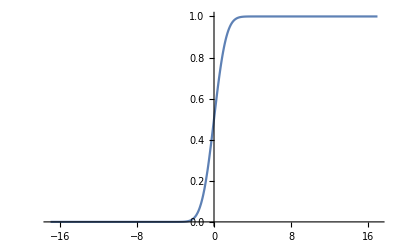

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
SurvivalFunction[NormalDistribution[0,1],x]
```

1/2 Erfc[x/(√2)]

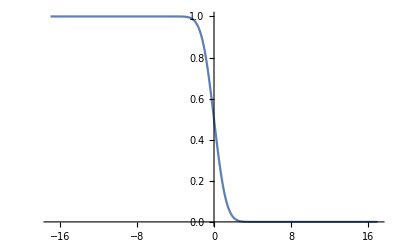

```mathematica
Plot[1/2 Erfc[x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

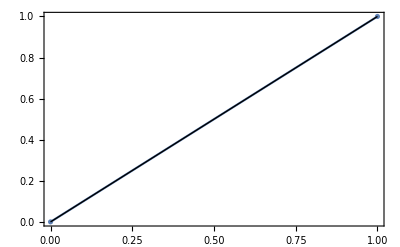

```mathematica
ProbabilityPlot[NormalDistribution[0,1]]
```

```mathematica
Kurtosis@NormalDistribution[]
```

3

```mathematica
WolframLanguageData["*Distribution"]
```

Missing[UnknownEntity,{WolframLanguageSymbol,*Distribution}]

```mathematica
WolframLanguageData["~Distribution"]
```

Missing[UnknownEntity,{WolframLanguageSymbol,~Distribution}]